## Numerical Fit Data

```mathematica
data=Import["/home/pratul/Downloads/Project/Analytical fits/New results/All_dataset_numfits_hyb_EccTD_xlow045_GM_SEOBNRv4_new.txt","Table"]
```

{{#,hybrid,q,eta,tshift,tmatch_amp,tmatch_freq,l0,e0},{1.,1355,1.,0.25,60.,-61.131,-1270.26,1.423,0.173},{2.,1356,1.,0.25,-35.,-30.2792,-3369.34,1.574,0.23},{3.,1357,1.,0.25,95.,-95.7229,-2280.85,0.451,0.322},{4.,1358,1.,0.25,50.,-50.8727,-545.853,-2.682,0.322},{5.,1359,1.,0.25,75.,-75.9144,-931.066,1.834,0.317},{6.,1360,1.,0.25,-85.,-50.2038,-2168.94,-0.395,0.416},{7.,1361,1.,0.25,-90.,-55.0928,-2012.11,-1.019,0.416},{8.,1362,1.,0.25,125.,-125.951,-1208.95,-0.507,0.483},{9.,1363,1.,0.25,95.,-95.9091,-828.86,-0.912,0.505},{10.,1364,2.,0.22222,0.,-30.1312,-4376.08,-0.181,0.172},{11.,1365,2.,0.22222,-85.,-125.074,-3448.13,-1.127,0.209},{12.,1366,2.,0.22222,-45.,-30.3449,-2467.68,-2.89,0.32},{13.,1367,2.,0.22222,60.,-61.2333,-1583.98,1.687,0.32},{14.,1368,2.,0.22222,-35.,-29.8486,-2900.13,0.42,0.324},{15.,1369,2.,0.22222,-165.,-29.7718,-2152.05,-0.203,0.478},{16.,1370,2.,0.22222,-225.,-295.128,-2001.21,3.063,0.508},{17.,1371,3.,0.1875,30.,-450.068,-5872.85,0.665,0.204},{18.,1372,3.,0.1875,35.,-35.933,-2207.17,3.005,0.3},{19.,1373,3.,0.1875,-105.,-29.9458,-1388.89,1.682,0.3},{20.,1374,3.,0.1875,-70.,-30.1714,-1388.89,3.114,0.495}}

```mathematica
sn=Flatten[data[[2;;,1;;1]]]
simVec=Flatten[data[[2;;,2;;2]]]
qVec=Flatten[data[[2;;,3;;3]]]
etaVec=Flatten[data[[2;;,4;;4]]]
tshiftVec=Flatten[data[[2;;,5;;5]]]
tmatch$ampVec=Flatten[data[[2;;,6;;6]]]
tmatch$freqVec=Flatten[data[[2;;,7;;7]]]
l0Vec=Flatten[data[[2;;,8;;8]]]
e0Vec=Flatten[data[[2;;,9;;9]]]
```

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.}

{1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,2.,2.,2.,2.,2.,2.,2.,3.,3.,3.,3.}

{0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.22222,0.22222,0.22222,0.22222,0.22222,0.22222,0.22222,0.1875,0.1875,0.1875,0.1875}

{60.,-35.,95.,50.,75.,-85.,-90.,125.,95.,0.,-85.,-45.,60.,-35.,-165.,-225.,30.,35.,-105.,-70.}

{-61.131,-30.2792,-95.7229,-50.8727,-75.9144,-50.2038,-55.0928,-125.951,-95.9091,-30.1312,-125.074,-30.3449,-61.2333,-29.8486,-29.7718,-295.128,-450.068,-35.933,-29.9458,-30.1714}

{-1270.26,-3369.34,-2280.85,-545.853,-931.066,-2168.94,-2012.11,-1208.95,-828.86,-4376.08,-3448.13,-2467.68,-1583.98,-2900.13,-2152.05,-2001.21,-5872.85,-2207.17,-1388.89,-1388.89}

{1.423,1.574,0.451,-2.682,1.834,-0.395,-1.019,-0.507,-0.912,-0.181,-1.127,-2.89,1.687,0.42,-0.203,3.063,0.665,3.005,1.682,3.114}

{0.173,0.23,0.322,0.322,0.317,0.416,0.416,0.483,0.505,0.172,0.209,0.32,0.32,0.324,0.478,0.508,0.204,0.3,0.3,0.495}

## Model Fits (based on sets with unique eccentricity)

### (Hinder+ inspired) Frequency (t_match model)

```mathematica
(*selects fits within 200M of the merger*)
```

```mathematica
simlist={1355,1356,1357,1358,0,1360,0,1362,0,1364,1365,1366,0,1368,1369,0,1371,0,1373,1374};
simlist=simVec;
idxlist ={};
For[k=1,k<21,k++,If[simVec[[k]]==simlist[[k]], AppendTo[idxlist,k]]]
idxlist
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Length[idxlist]
```

20

```mathematica
etaVec=etaVec[[idxlist]];
qVec=qVec[[idxlist]];
e0Vec=e0Vec[[idxlist]];
l0Vec=l0Vec[[idxlist]];
tmatch$freqVec=tmatch$freqVec[[idxlist]];
tmatch$ampVec=tmatch$ampVec[[idxlist]];
tshiftVec=tshiftVec[[idxlist]];
```

```mathematica
numfit=Table[{etaVec[[i]],e0Vec[[i]],l0Vec[[i]],tmatch$freqVec[[i]]},{i,1,Length[etaVec]}]
```

{{0.25,0.173,1.423,-1270.26},{0.25,0.23,1.574,-3369.34},{0.25,0.322,0.451,-2280.85},{0.25,0.322,-2.682,-545.853},{0.25,0.317,1.834,-931.066},{0.25,0.416,-0.395,-2168.94},{0.25,0.416,-1.019,-2012.11},{0.25,0.483,-0.507,-1208.95},{0.25,0.505,-0.912,-828.86},{0.22222,0.172,-0.181,-4376.08},{0.22222,0.209,-1.127,-3448.13},{0.22222,0.32,-2.89,-2467.68},{0.22222,0.32,1.687,-1583.98},{0.22222,0.324,0.42,-2900.13},{0.22222,0.478,-0.203,-2152.05},{0.22222,0.508,3.063,-2001.21},{0.1875,0.204,0.665,-5872.85},{0.1875,0.3,3.005,-2207.17},{0.1875,0.3,1.682,-1388.89},{0.1875,0.495,3.114,-1388.89}}

```mathematica
FitFunc =FindFit[numfit,{a0+a1*η+a2*η^2+b1*e+b2*e^2+b3*e^3+c1 e η+c2 e^2 η+c3*e*η^2+c4*e^2*η^2+c5*e^3*η(*+c6*e^3*η^2*)+d1 e η Cos[l+d2]+d3 e^2 η^2 Cos[l+d4]+d5 e^3 η Cos[e l+d6]+d7 e^3 η^2 Cos[e l+d8]},{a0,a1,a2,b1,b2,b3,c1,c2,c3,c4,c5,(*c6,*) d1,d2,d3,d4, d5, d6,d7, d8},{η,e,l}]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a0→-569916.,a1→2.8807×10^6,a2→-1.92589×10^6,b1→4.96114×10^6,b2→-1.35043×10^7,b3→1.20704×10^7,c1→-2.39782×10^7,c2→6.00997×10^7,c3→1.15905×10^7,c4→-1.03762×10^7,c5→-5.13849×10^7,d1→84783.1,d2→264.595,d3→1.51329×10^6,d4→1819.75,d5→-1.36416×10^6,d6→2320.57,d7→5.96784×10^6,d8→9652.7}

```mathematica
(*NOTE. circular cubic eta terms may not be useful due to low mass ratio cases under consideration*)
```

```mathematica
model=a0+a1*ηη+a2*ηη^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*ηη+c2*ee^2*ηη+c3*ee*ηη^2+c4*ee^2*ηη^2+c5*ee^3*ηη(*+c6*ee^3*ηη^2*)+d1 ee ηη Cos[ll+d2]+d3 ee^2 ηη^2 Cos[ll+d4]+d5 ee^3 ηη Cos[ee ll+d6]+d7 ee^3 ηη^2 Cos[ee ll+d8]/.{ηη->etaVec,ee->e0Vec,ll->l0Vec}/.FitFunc
```

{-1313.9,-3237.91,-2500.33,-468.539,-885.913,-2056.33,-2060.31,-1095.63,-870.899,-4362.42,-3483.45,-2485.34,-1700.36,-2696.56,-2137.03,-1978.92,-5858.49,-2246.53,-1357.06,-1397.24}

```mathematica
res=tmatch$freqVec-model
Max[Abs[res]]
Mean[Abs[res]]
Quantile[Abs[res],{0.5,0.75,0.85,0.95}]
err=res.res
```

{43.6425,-131.438,219.48,-77.3145,-45.1525,-112.605,48.2066,-113.322,42.0386,-13.663,35.3159,17.6643,116.378,-203.565,-15.0266,-22.289,-14.3585,39.3602,-31.8235,8.35408}

219.48

67.5499

{42.0386,112.605,116.378,203.565}

165271.

```mathematica
(*75% simulations have fits within 30M.. *)
```

```mathematica
(*snum={};For[i=1,i<21,i++,snum=AppendTo[snum,ToString[i]]]*)
```

```mathematica
tmatch$freqVec
```

{-1270.26,-3369.34,-2280.85,-545.853,-931.066,-2168.94,-2012.11,-1208.95,-828.86,-4376.08,-3448.13,-2467.68,-1583.98,-2900.13,-2152.05,-2001.21,-5872.85,-2207.17,-1388.89,-1388.89}

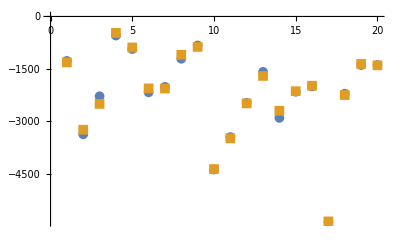

```mathematica
ListPlot[{tmatch$freqVec,model},PlotMarkers->{Automatic,10
}]
```

```mathematica
fitrule$tmatch$freq=FitFunc
```

{a0→-569916.,a1→2.8807×10^6,a2→-1.92589×10^6,b1→4.96114×10^6,b2→-1.35043×10^7,b3→1.20704×10^7,c1→-2.39782×10^7,c2→6.00997×10^7,c3→1.15905×10^7,c4→-1.03762×10^7,c5→-5.13849×10^7,d1→84783.1,d2→264.595,d3→1.51329×10^6,d4→1819.75,d5→-1.36416×10^6,d6→2320.57,d7→5.96784×10^6,d8→9652.7}

### TEST (freq model)

Model should produce a negative t_match for values for (e_ 0 , q, l_ 0) in the calibration range or at least the range of values the model is expected to work well. We choose this range as e_ 0 (0.01 - 0.2), q (1 - 3) and l_ 0 (-π, π).

```mathematica
e0testVec=Table[e0,{e0,0.1,0.2,0.000001}];
qtestVec=Range[1,3,0.00001];
etatestVec=qtestVec/(1+qtestVec)^2;
l0testVec=N[Range[-π,π,π/100000]];
```

```mathematica
Length[e0testVec]
```

100001

```mathematica
Length[qtestVec]
```

200001

```mathematica
Length[l0testVec]
```

200001

```mathematica
e0testVecNew=e0testVec[[SeedRandom[1234];RandomInteger[{1,Length[e0testVec]},10000]]];
```

```mathematica
qtestVecNew = qtestVec[[SeedRandom[1234];RandomInteger[{1,Length[etatestVec]},10000]]];
```

```mathematica
etafromq = qtestVecNew/(1+qtestVecNew)^2;
```

```mathematica
etatestVecNew=etatestVec[[SeedRandom[1234];RandomInteger[{1,Length[etatestVec]},10000]]];
```

```mathematica
l0testVecNew=l0testVec[[SeedRandom[1234];RandomInteger[{1,Length[l0testVec]},10000]]];
```

```mathematica
e0testVecNew;
```

```mathematica
qtestVecNew;
```

```mathematica
etafromq -etatestVecNew;
```

```mathematica
etatestVecNew;
```

```mathematica
l0testVecNew;
```

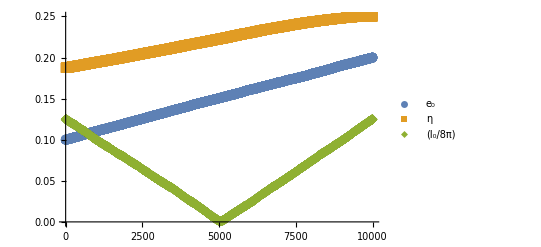

```mathematica
ListPlot[{Sort[e0testVecNew],Sort[etatestVecNew],Abs[Sort[l0testVecNew]]/(8π)},PlotMarkers->{Automatic,10},PlotLegends->{"e_0","η","(l_0/8π)"}]
```

```mathematica
model=a0+a1*ηη+a2*ηη^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*ηη+c2*ee^2*ηη+c3*ee*ηη^2+c4*ee^2*ηη^2+c5*ee^3*ηη(*+c6*ee^3*ηη^2*)+d1 ee ηη Cos[ll+d2]+d3 ee^2 ηη^2 Cos[ll+d4]+d5 ee^3 ηη Cos[ee ll+d6]+d7 ee^3 ηη^2 Cos[ee ll+d8]/.{ηη->etatestVecNew,ee->e0testVecNew,ll->l0testVecNew}/.FitFunc;
```

```mathematica
testidxlist ={};
For[k=1,k<10001,k++,If[model[[k]]>0, AppendTo[testidxlist,k]]]
testidxlist;
```

```mathematica
e0testVecNew[[testidxlist]];
```

```mathematica
qtestVecNew[[testidxlist]];
```

```mathematica
etafromq[[testidxlist]]-etatestVecNew[[testidxlist]];
```

```mathematica
etatestVecNew[[testidxlist]];
```

```mathematica
l0testVecNew[[testidxlist]];
```

```mathematica
Length[testidxlist]
```

1277

```mathematica
testidxlist2={};
For[k=1,k<10001,k++,If[model[[k]]<0, AppendTo[testidxlist2,k]]]
testidxlist2;
```

```mathematica
Length[testidxlist2]
```

8723

### (Hinder+ inspired) Amplitude (t_match model)

```mathematica
numfit=Table[{etaVec[[i]],e0Vec[[i]],l0Vec[[i]],tmatch$ampVec[[i]]},{i,1,Length[etaVec]}]
```

{{0.25,0.173,1.423,-61.131},{0.25,0.23,1.574,-30.2792},{0.25,0.322,0.451,-95.7229},{0.25,0.322,-2.682,-50.8727},{0.25,0.317,1.834,-75.9144},{0.25,0.416,-0.395,-50.2038},{0.25,0.416,-1.019,-55.0928},{0.25,0.483,-0.507,-125.951},{0.25,0.505,-0.912,-95.9091},{0.22222,0.172,-0.181,-30.1312},{0.22222,0.209,-1.127,-125.074},{0.22222,0.32,-2.89,-30.3449},{0.22222,0.32,1.687,-61.2333},{0.22222,0.324,0.42,-29.8486},{0.22222,0.478,-0.203,-29.7718},{0.22222,0.508,3.063,-295.128},{0.1875,0.204,0.665,-450.068},{0.1875,0.3,3.005,-35.933},{0.1875,0.3,1.682,-29.9458},{0.1875,0.495,3.114,-30.1714}}

```mathematica
FitFunc =FindFit[numfit,{a0+a1*η+a2*η^2+b1*e+b2*e^2+b3*e^3+c1 e η+c2 e^2 η+c3*e*η^2+c4*e^2*η^2+c5*e^3*η(*+c6*e^3*η^2*)+d1 e η Cos[l+d2]+d3 e^2 η^2 Cos[l+d4]+d5 e^3 η Cos[e l+d6]},{a0,a1,a2,b1,b2,b3,c1,c2,c3,c4,c5(*,c6*),d1,d2,d3,d4,d5,d6},{η,e,l}]
```

{a0→-30423.7,a1→347683.,a2→-908464.,b1→69809.2,b2→309306.,b3→-651233.,c1→-1.52253×10^6,c2→348354.,c3→4.9989×10^6,c4→-6.3776×10^6,c5→2.59743×10^6,d1→1994.68,d2→959.205,d3→-28546.1,d4→-10928.5,d5→1200.93,d6→-279.986}

```mathematica
model=a0+a1*ηη+a2*ηη^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*ηη+c2*ee^2*ηη+c3*ee*ηη^2+c4*ee^2*ηη^2+c5*ee^3*ηη(*+c6*ee^3*ηη^2*)+d1 ee ηη Cos[ll+d2]+d3 ee^2 ηη^2 Cos[ll+d4]+d5 ee^3 ηη Cos[ee ll+d6]/.{ηη->etaVec,ee->e0Vec,ll->l0Vec}/.FitFunc
```

{-57.4041,-40.1263,-71.5216,-52.0278,-85.4966,-74.8052,-43.6445,-115.713,-100.338,-29.8248,-125.765,-30.3765,-47.6851,-43.1674,-29.3299,-295.383,-450.068,-32.9374,-32.9413,-30.1714}

```mathematica
res=tmatch$ampVec-model
Max[Abs[res]]
Quantile[Abs[res],{0.5,0.75,0.85,0.95}]
err=res.res
```

{-3.72695,9.84714,-24.2012,1.15512,9.58215,24.6014,-11.4483,-10.2383,4.42897,-0.306389,0.691303,0.0315143,-13.5482,13.3188,-0.44199,0.255045,3.9563×10^-11,-2.99554,2.99554,-1.42361×10^-10}

24.6014

{2.99554,10.2383,13.3188,24.2012}

2030.16

```mathematica
(*90% of fits (18) have res better than 10M*)
```

```mathematica
fitrule$tmatch$amp=FitFunc
```

{a0→-30423.7,a1→347683.,a2→-908464.,b1→69809.2,b2→309306.,b3→-651233.,c1→-1.52253×10^6,c2→348354.,c3→4.9989×10^6,c4→-6.3776×10^6,c5→2.59743×10^6,d1→1994.68,d2→959.205,d3→-28546.1,d4→-10928.5,d5→1200.93,d6→-279.986}

```mathematica
tmatch$ampVec
```

{-61.131,-30.2792,-95.7229,-50.8727,-75.9144,-50.2038,-55.0928,-125.951,-95.9091,-30.1312,-125.074,-30.3449,-61.2333,-29.8486,-29.7718,-295.128,-450.068,-35.933,-29.9458,-30.1714}

```mathematica
model
```

{-57.4041,-40.1263,-71.5216,-52.0278,-85.4966,-74.8052,-43.6445,-115.713,-100.338,-29.8248,-125.765,-30.3765,-47.6851,-43.1674,-29.3299,-295.383,-450.068,-32.9374,-32.9413,-30.1714}

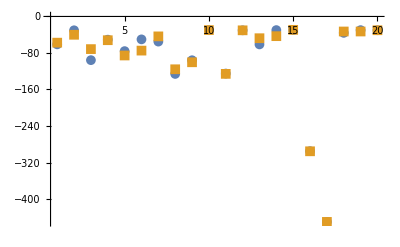

```mathematica
ListPlot[{tmatch$ampVec,model},PlotMarkers->{Automatic,10},PlotRange->All]
```

### TEST (amp model)

Model should produce a negative t_match for values for (e_ 0 , q, l_ 0) in the calibration range or at least the range of values the model is expected to work well. We choose this range as e_ 0 (0.01 - 0.2), q (1 - 3) and l_ 0 (-π,  π).

```mathematica
model=a0+a1*ηη+a2*ηη^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*ηη+c2*ee^2*ηη+c3*ee*ηη^2+c4*ee^2*ηη^2+c5*ee^3*ηη(*+c6*ee^3*ηη^2*)+d1 ee ηη Cos[ll+d2]+d3 ee^2 ηη^2 Cos[ll+d4]+d5 ee^3 ηη Cos[ee ll+d6]/.{ηη->etatestVecNew,ee->e0testVecNew,ll->l0testVecNew}/.FitFunc;
```

```mathematica
testidxlist3={};
For[k=1,k<10001,k++,If[model[[k]]>0, AppendTo[testidxlist3,k]]]
testidxlist3;
```

```mathematica
Length[testidxlist3]
```

4008

```mathematica
testidxlist4={};
For[k=1,k<10001,k++,If[model[[k]]<0, AppendTo[testidxlist4,k]]]
testidxlist4;
```

```mathematica
Length[testidxlist4]
```

5992

```mathematica
idxlistformismatch=Intersection[testidxlist2,testidxlist4];
```

```mathematica
Length[idxlistformismatch]
```

5040

```mathematica
Sort[e0testVecNew[[idxlistformismatch]]];
```

```mathematica
Sort[qtestVecNew[[idxlistformismatch]]];
```

```mathematica
Sort[etafromq[[idxlistformismatch]]];
```

```mathematica
Sort[etatestVecNew[[idxlistformismatch]]];
```

```mathematica
Sort[etafromq[[idxlistformismatch]]]-Sort[etatestVecNew[[idxlistformismatch]]];
```

```mathematica
Sort[l0testVecNew[[idxlistformismatch]]];
```

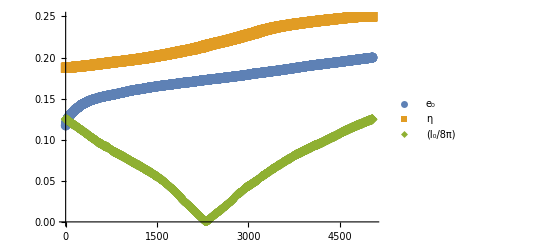

```mathematica
ListPlot[{Sort[e0testVecNew[[idxlistformismatch]]],Sort[etatestVecNew[[idxlistformismatch]]],Abs[Sort[l0testVecNew[[idxlistformismatch]]]]/(8π)},PlotMarkers->{Automatic,10},PlotLegends->{"e_0","η","(l_0/8π)"}]
```

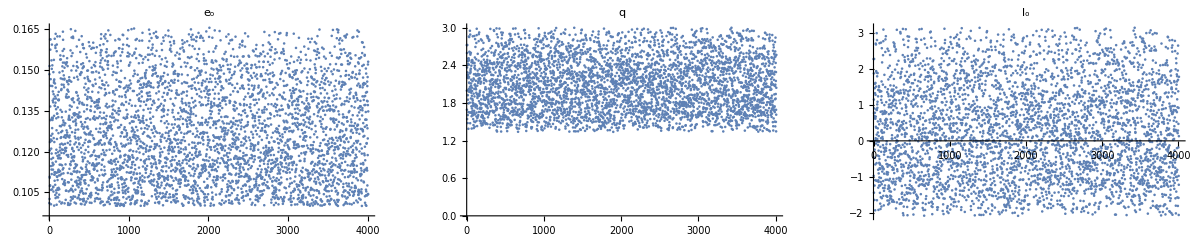

```mathematica
p1=ListPlot[e0testVecNew[[testidxlist3]],PlotLabel->"e_o"];
p2=ListPlot[qtestVecNew[[testidxlist3]],PlotLabel->"q"];
p3 = ListPlot[l0testVecNew[[testidxlist3]],PlotLabel->"l_o"];
GraphicsRow[{p1,p2,p3},ImageSize->Full]
```

```mathematica
e0testVecNew[[idxlistformismatch]]; (* use these values for e0 *)
```

```mathematica
qtestVecNew[[idxlistformismatch]]; (* use these values for q *)
```

```mathematica
etatestVecNew[[idxlistformismatch]]; (* use these values for eta *)
```

```mathematica
l0testVecNew[[idxlistformismatch]] ;(* use these values for l0 *)
```

```mathematica
etafromq[[idxlistformismatch]]-etatestVecNew[[idxlistformismatch]];
```

```mathematica
(*dat1=Flatten/@Transpose[{qtestVecNew[[idxlistformismatch]],etatestVecNew[[idxlistformismatch]],e0testVecNew[[idxlistformismatch]],l0testVecNew[[idxlistformismatch]]}];
Export["physical_data_10kpts.txt",dat1,"Table"]*)
```

### (Hinder+ inspired) t-shift (e, q, l) model

```mathematica
numfit=Table[{qVec[[i]],e0Vec[[i]],l0Vec[[i]],tshiftVec[[i]]},{i,1,Length[etaVec]}]
```

{{1.,0.173,1.423,60.},{1.,0.23,1.574,-35.},{1.,0.322,0.451,95.},{1.,0.322,-2.682,50.},{1.,0.317,1.834,75.},{1.,0.416,-0.395,-85.},{1.,0.416,-1.019,-90.},{1.,0.483,-0.507,125.},{1.,0.505,-0.912,95.},{2.,0.172,-0.181,0.},{2.,0.209,-1.127,-85.},{2.,0.32,-2.89,-45.},{2.,0.32,1.687,60.},{2.,0.324,0.42,-35.},{2.,0.478,-0.203,-165.},{2.,0.508,3.063,-225.},{3.,0.204,0.665,30.},{3.,0.3,3.005,35.},{3.,0.3,1.682,-105.},{3.,0.495,3.114,-70.}}

```mathematica
FitFunc =FindFit[numfit,{a0+a1*q+a2*q^2+b1*e+b2*e^2+b3*e^3+c1 e q+c2 e^2 q+c3*e*q^2+c4*e^2*q^2+c5*e^3*q(*+c6*e^3*q^2*)+d1 e q Cos[l+d2]+d3 e^2 q^2 Cos[e l+d4]+d5 e^3 q Cos[l+d6]+d7 e q^2 Cos[l+d8]},{a0,a1,a2,b1,b2,b3,c1,c2,c3, c4,c5,(*c6,*)d1,d2,d3,d4,d5,d6,d7,d8},{q,e,l}]
```

{a0→1075.55,a1→-8517.76,a2→6789.44,b1→74899.9,b2→-433054.,b3→611459.,c1→-19087.5,c2→292870.,c3→-40785.6,c4→57382.9,c5→-498349.,d1→-2948.6,d2→-15.0158,d3→-8260.27,d4→34.5353,d5→27184.3,d6→-102.895,d7→-708.861,d8→12.2701}

```mathematica
model=a0+a1*qq+a2*qq^2+b1*ee+b2*ee^2+b3*ee^3+c1*ee*qq+c2*ee^2*qq+c3*ee*qq^2+c4*ee^2*qq^2+c5*ee^3*qq(*+c6*ee^3*qq^2*)+d1 ee qq Cos[ll+d2]+d3 ee^2 qq^2 Cos[ee ll+d4]+d5 ee^3 qq Cos[ll+d6]+d7 ee qq^2 Cos[ll+d8]/.FitFunc/.{qq->qVec,ee->e0Vec,ll->l0Vec}
```

{61.4235,-37.4649,90.3503,55.2966,73.2219,-53.4078,-111.291,102.472,109.4,-0.109464,-84.8168,-45.7613,60.8983,-35.2664,-164.824,-225.12,30.,35.3343,-105.334,-70.}

```mathematica
res=Abs[tshiftVec-model]
Max[Abs[res]]
Quantile[Abs[res],{0.5,0.75,0.85,0.95}]
err=res.res
```

{1.42347,2.46493,4.64966,5.29658,1.77806,31.5922,21.2914,22.5279,14.3998,0.109464,0.18319,0.761252,0.898271,0.266427,0.175644,0.119961,1.09139×10^-11,0.334313,0.334313,2.72848×10^-11}

31.5922

{0.761252,4.64966,14.3998,22.5279}

2228.96

```mathematica
(*95% of fits have res better than 10M*)
```

```mathematica
fitrule$tshift=FitFunc
```

{a0→1075.55,a1→-8517.76,a2→6789.44,b1→74899.9,b2→-433054.,b3→611459.,c1→-19087.5,c2→292870.,c3→-40785.6,c4→57382.9,c5→-498349.,d1→-2948.6,d2→-15.0158,d3→-8260.27,d4→34.5353,d5→27184.3,d6→-102.895,d7→-708.861,d8→12.2701}

```mathematica
e0Vec
```

{0.173,0.23,0.322,0.322,0.317,0.416,0.416,0.483,0.505,0.172,0.209,0.32,0.32,0.324,0.478,0.508,0.204,0.3,0.3,0.495}

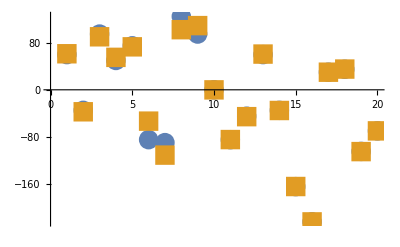

```mathematica
ListPlot[{tshiftVec,model},PlotMarkers->{Automatic,20}]
```